```mathematica
$PlotTheme="Scientific"
```

Scientific

## Toy Model

We define the series

```mathematica
SN[NN_] := Sum[1/(n+1)(9/10)^n,{n,1,NN}]
```

The actual value of the series is

```mathematica
S = SN[∞]
```

1/9 (-9+10 Log[10])

Numerical value

```mathematica
N[S,4]
```

1.558

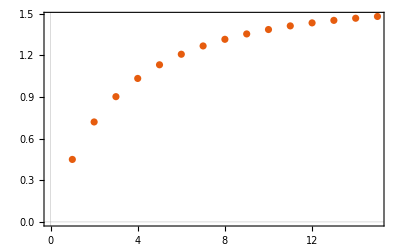

```mathematica
ListPlot[Table[SN[NN],{NN,1,15}]]
```

We assume N=15 is the max cut-off we can obtain. The largest three cut-offed sums we can compute are

```mathematica
Print[SN[15]," ~ ", N[SN[15],4]]
Print[SN[14]," ~ ", N[SN[14],4]]
Print[SN[13]," ~ ", N[SN[13],4]]
```

23703901684627396833/16016000000000000000 ~ 1.48

183576598917192603/125125000000000000 ~ 1.467

29066926903451937/20020000000000000 ~ 1.452

```mathematica
N[100*(1-SN[15]/S),2]
```

5.

Where the last value  1.480 is 5% away from the series value.

The coefficients aN are given by

```mathematica
aN[n_]:= 1/(n+1)(9/10)^n
```

And the ratios

```mathematica
cN[NN_]:= aN[NN]/aN[NN-1]
```

```mathematica
ratios=Table[{NN,cN[NN]},{NN,1,15}]
```

{{1,9/20},{2,3/5},{3,27/40},{4,18/25},{5,3/4},{6,27/35},{7,63/80},{8,4/5},{9,81/100},{10,9/11},{11,33/40},{12,54/65},{13,117/140},{14,21/25},{15,27/32}}

```mathematica
fit=Fit[ratios,{1,x^(-1),x^(-2)},x]
```

0.889228+0.303113/x^2-0.741398/x

```mathematica
L= Limit[fit,x->∞]
```

0.889228

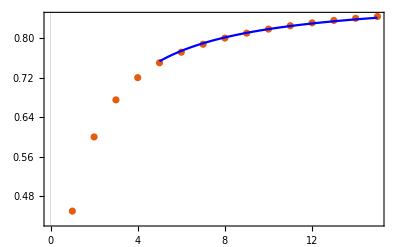

```mathematica
Show[ListPlot[ratios],Plot[fit,{x,5,15},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(SN[15]SN[13]-SN[14]^2)/(SN[15]-2SN[14]+SN[13])
```

3877629001570595709/2502500000000000000

```mathematica
N[LB,4]
```

1.55

```mathematica
N[100*(1-LB/S),1]
```

0.6

only 0.6% away from the value of the series.

The estimate for the upper bound is given by

```mathematica
UB=(SN[15] - L SN[14])/(1-L)
```

1.58331

```mathematica
N[UB,4]
```

1.58331

```mathematica
N[100*(UB/S-1),1]
```

1.59687

only 1.6% away from the value of the series.

## Boundary spins j = 1 and γ = 1.2

We import the CSV data into the appropriate columns

```mathematica
ROOTDIR = NotebookDirectory[];
```

```mathematica
{Ai0,Ai1,Ai2}=Transpose[Import[ROOTDIR<>"Delta_4_ampls/Immirzi_1.2/j_1.0/CSV_format/Delta_4_ampls_Dl_max_25.csv","Table"]];
```

### Boundary intertwiners i = 2

```mathematica
Ai2
```

{2.02191×10^-37,1.09032×10^-36,2.03264×10^-36,2.59232×10^-36,2.90128×10^-36,3.08743×10^-36,3.20956×10^-36,3.29512×10^-36,3.35803×10^-36,3.4058×10^-36,3.44301×10^-36,3.47247×10^-36,3.49617×10^-36,3.51544×10^-36,3.53128×10^-36,3.54445×10^-36,3.55549×10^-36,3.56483×10^-36,3.5728×10^-36,3.57966×10^-36,3.58559×10^-36,3.59077×10^-36,3.59531×10^-36,3.59931×10^-36,3.60286×10^-36,3.60603×10^-36}

```mathematica
ai2n[DL_]:=If[DL==0, Ai2[[1]],Ai2[[DL+1]]-Ai2[[DL]]]
```

```mathematica
ci2n[DL_]:=ai2n[DL]/ai2n[DL-1]
```

```mathematica
ratios=Table[{DL,ci2n[DL]},{DL,1,25}]
```

{{1,4.3925},{2,1.06103},{3,0.593934},{4,0.552037},{5,0.602494},{6,0.656083},{7,0.700583},{8,0.735289},{9,0.759268},{10,0.778946},{11,0.792019},{12,0.803943},{13,0.813385},{14,0.822347},{15,0.830821},{16,0.838484},{17,0.846313},{18,0.853041},{19,0.86004},{20,0.865917},{21,0.871983},{22,0.877093},{23,0.882257},{24,0.886704},{25,0.891073}}

```mathematica
preLB =(Ai2[[16]]Ai2[[14]]-Ai2[[15]]^2)/(Ai2[[16]]-2Ai2[[15]]+Ai2[[14]])
```

3.60911×10^-36

```mathematica
fit=Fit[ratios[[5;;16]],{1,x^(-1),x^(-2)},x]
```

0.936971-0.762647/x^2-1.53184/x

```mathematica
preL= Limit[fit,x->∞]
```

0.936971

```mathematica
preUB=(Ai2[[16]] - preL Ai2[[15]])/(1-preL)
```

3.74017×10^-36

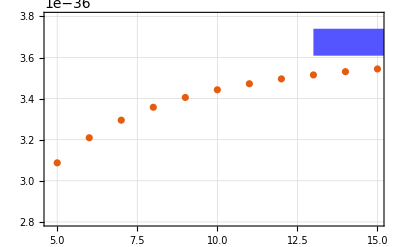

```mathematica
Ai2plot=ListPlot[Transpose[{Range[5,15],Ai2[[6;;16]]}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{13,preLB},{16,preUB}]},PlotRange->{Automatic,{2.8 10^(-36),3.8 10^(-36)}}]
```

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.962847+0.84655/x^2-1.96573/x

```mathematica
L= Limit[fit,x->∞]
```

0.962847

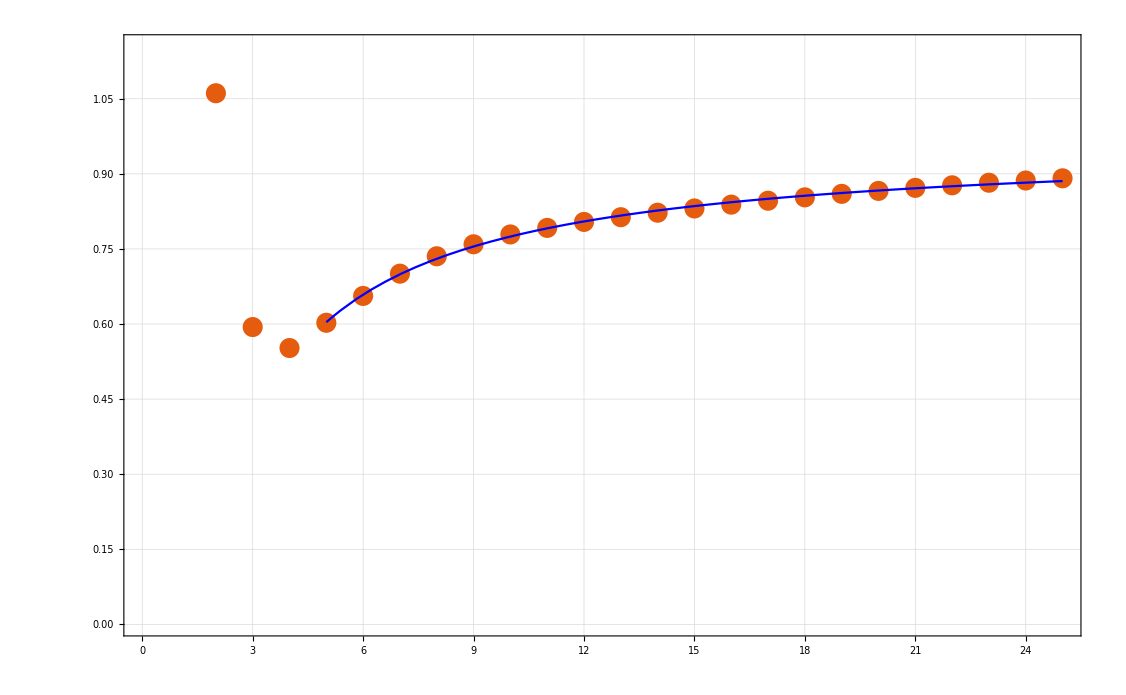

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai2[[-1]]Ai2[[-3]]-Ai2[[-2]]^2)/(Ai2[[-1]]-2Ai2[[-2]]+Ai2[[-3]])
```

3.63191×10^-36

The estimate for the upper bound is given by

```mathematica
UB=(Ai2[[-1]] - L Ai2[[-2]])/(1-L)
```

3.68804×10^-36

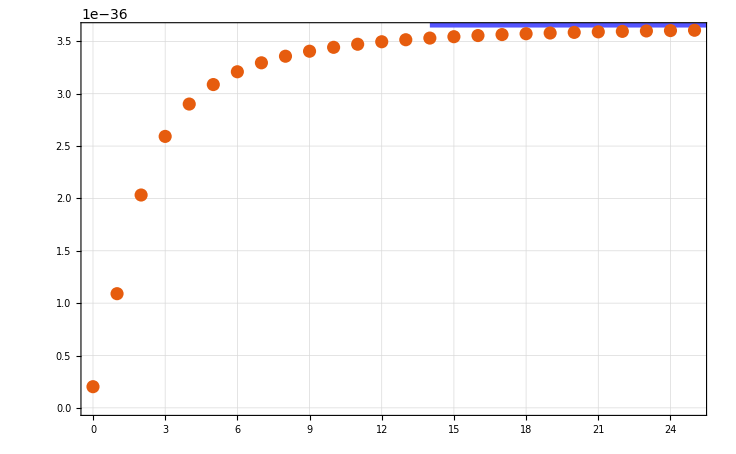

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai2}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

```mathematica
Export[ROOTDIR<>"Plots/Plotg12j1i2.svg",Ai2plot]
```

/home/pdona/Dropbox/Ongoing Projects/HowToSpinFoamAmplitude/HowToSpinFoamAmplitude/Plots/Plotg12j1i2.svg

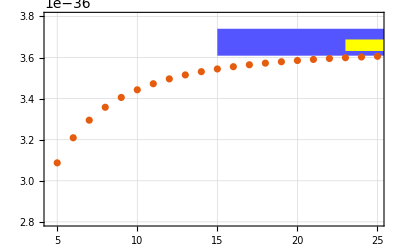

```mathematica
Ai2plot=ListPlot[Transpose[{Range[5,25],Ai2[[6;;]]}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{15,preLB},{26,preUB}],Yellow,Rectangle[{23,LB},{26,UB}]},PlotRange->{Automatic,{2.8 10^(-36),3.8 10^(-36)}}]
```

### Boundary intertwiners i = 1

```mathematica
Ai1
```

{3.70797×10^-38,1.83833×10^-37,3.21386×10^-37,3.95264×10^-37,4.31891×10^-37,4.52113×10^-37,4.64769×10^-37,4.73539×10^-37,4.80034×10^-37,4.85013×10^-37,4.8893×10^-37,4.92049×10^-37,4.94566×10^-37,4.96616×10^-37,4.98301×10^-37,4.99698×10^-37,5.00868×10^-37,5.01855×10^-37,5.02695×10^-37,5.03415×10^-37,5.04037×10^-37,5.04578×10^-37,5.05051×10^-37,5.05468×10^-37,5.05837×10^-37,5.06166×10^-37}

```mathematica
ai1n[DL_]:=If[DL==0, Ai1[[1]],Ai1[[DL+1]]-Ai1[[DL]]]
```

```mathematica
ci1n[DL_]:=ai1n[DL]/ai1n[DL-1]
```

```mathematica
ratios=Table[{DL,ci1n[DL]},{DL,1,25}]
```

{{1,3.95777},{2,0.937312},{3,0.537088},{4,0.49577},{5,0.552129},{6,0.625845},{7,0.692882},{8,0.740648},{9,0.766712},{10,0.786467},{11,0.796497},{12,0.806846},{13,0.814319},{14,0.822078},{15,0.82971},{16,0.836559},{17,0.844234},{18,0.850494},{19,0.857731},{20,0.86343},{21,0.869906},{22,0.875039},{23,0.880632},{24,0.885216},{25,0.889943}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.932938-3.62262/x^2-1.18009/x

```mathematica
L= Limit[fit,x->∞]
```

0.932938

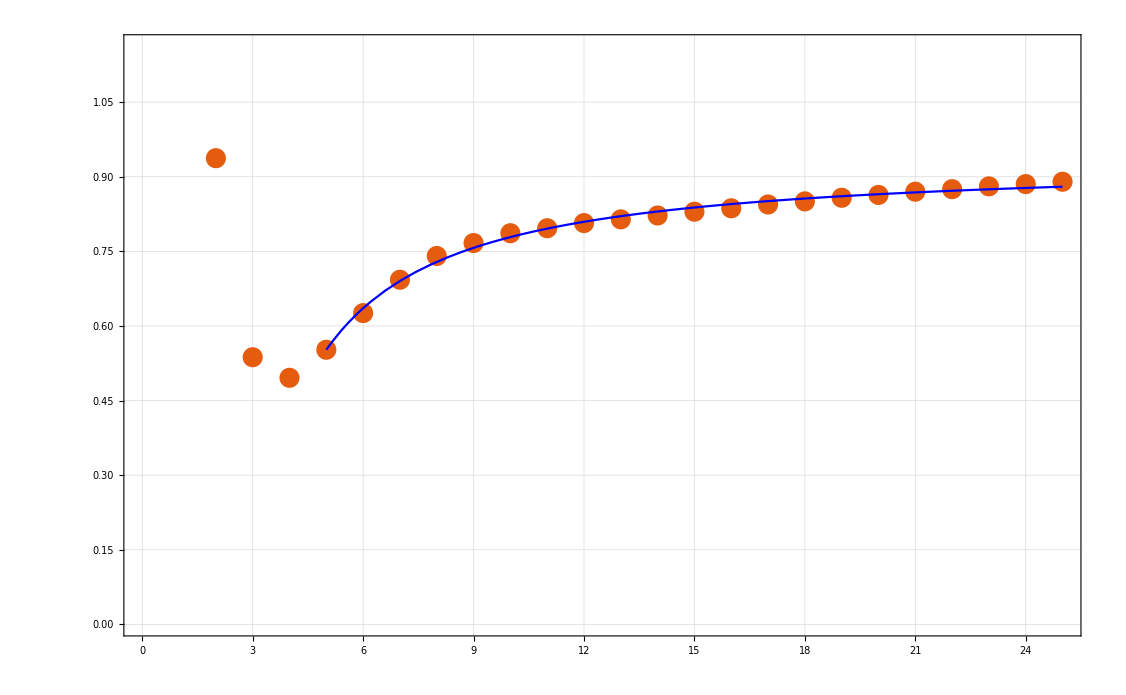

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai1[[-1]]Ai1[[-3]]-Ai1[[-2]]^2)/(Ai1[[-1]]-2Ai1[[-2]]+Ai1[[-3]])
```

5.08821×10^-37

The estimate for the upper bound is given by

```mathematica
UB=(Ai1[[-1]] - L Ai1[[-2]])/(1-L)
```

5.10734×10^-37

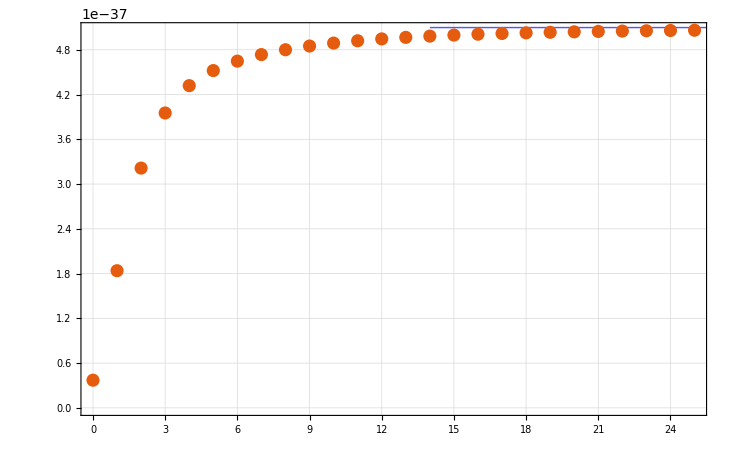

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

### Boundary intertwiners i = 0

```mathematica
Ai0
```

{7.7684×10^-39,4.28146×10^-38,8.53782×10^-38,1.15625×10^-37,1.35431×10^-37,1.48838×10^-37,1.58213×10^-37,1.64978×10^-37,1.70004×10^-37,1.73828×10^-37,1.76805×10^-37,1.79164×10^-37,1.81064×10^-37,1.82615×10^-37,1.83896×10^-37,1.84966×10^-37,1.85868×10^-37,1.86635×10^-37,1.87293×10^-37,1.87862×10^-37,1.88357×10^-37,1.8879×10^-37,1.8917×10^-37,1.89507×10^-37,1.89807×10^-37,1.90074×10^-37}

```mathematica
ai0n[DL_]:=If[DL==0, Ai0[[1]],Ai0[[DL+1]]-Ai0[[DL]]]
```

```mathematica
ci0n[DL_]:=ai0n[DL]/ai0n[DL-1]
```

```mathematica
ratios=Table[{DL,ci0n[DL]},{DL,1,25}]
```

{{1,4.51138},{2,1.2145},{3,0.710634},{4,0.654813},{5,0.676873},{6,0.699308},{7,0.721624},{8,0.742843},{9,0.760965},{10,0.778561},{11,0.792292},{12,0.805365},{13,0.816135},{14,0.826139},{15,0.835152},{16,0.843186},{17,0.850889},{18,0.85752},{19,0.864087},{20,0.869654},{21,0.875228},{22,0.879976},{23,0.884709},{24,0.888819},{25,0.892856}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.9902+5.6269/x^2-2.68768/x

```mathematica
L= Limit[fit,x->∞]
```

0.9902

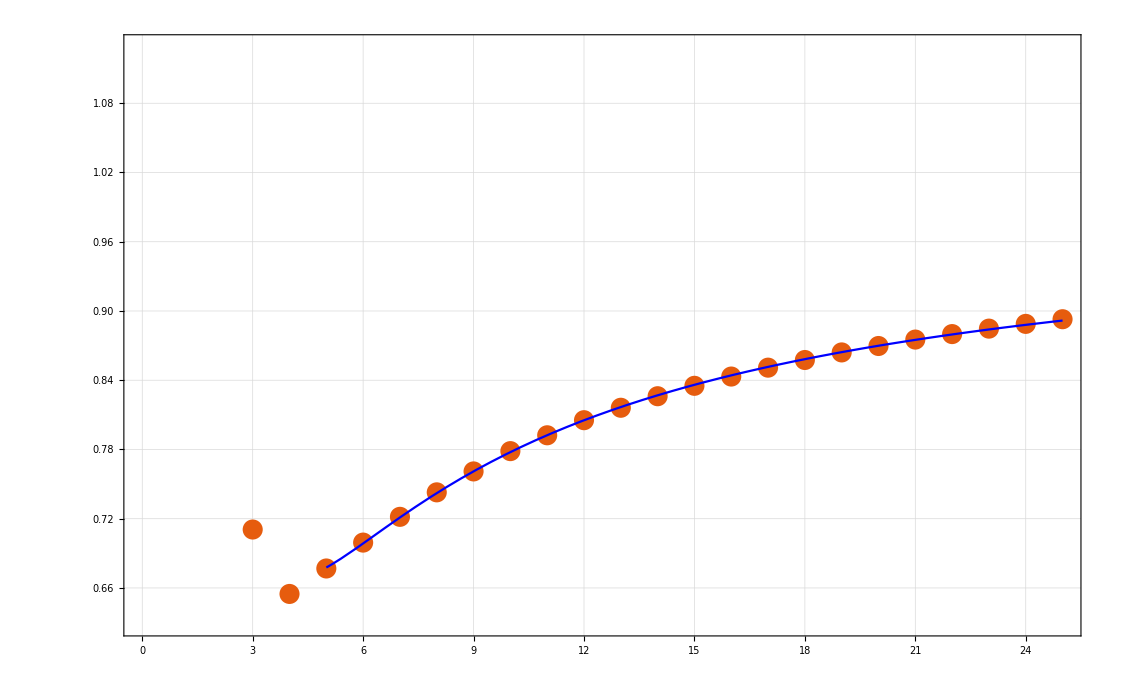

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai0[[-1]]Ai0[[-3]]-Ai0[[-2]]^2)/(Ai0[[-1]]-2Ai0[[-2]]+Ai0[[-3]])
```

1.92303×10^-37

The estimate for the upper bound is given by

```mathematica
UB=(Ai0[[-1]] - L Ai0[[-2]])/(1-L)
```

2.17096×10^-37

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

-Graphics-

## Boundary spins j = 1 and γ = 1.0

We import the CSV data into the appropriate columns

```mathematica
ROOTDIR = NotebookDirectory[];
```

```mathematica
{Ai0,Ai1,Ai2}=Transpose[Import[ROOTDIR<>"Delta_4_ampls/Immirzi_1.0/j_1.0/CSV_format/Delta_4_ampls_Dl_max_25.csv","Table"]];
```

### Boundary intertwiners i = 2

```mathematica
Ai2
```

{5.27118×10^-35,2.75497×10^-34,5.16261×10^-34,6.68525×10^-34,7.55624×10^-34,8.0788×10^-34,8.41413×10^-34,8.6435×10^-34,8.80825×10^-34,8.93117×10^-34,9.02572×10^-34,9.10011×10^-34,9.15979×10^-34,9.20837×10^-34,9.24846×10^-34,9.28188×10^-34,9.31004×10^-34,9.33395×10^-34,9.35442×10^-34,9.37208×10^-34,9.3874×10^-34,9.40078×10^-34,9.41253×10^-34,9.4229×10^-34,9.4321×10^-34,9.44029×10^-34}

```mathematica
ai2n[DL_]:=If[DL==0, Ai2[[1]],Ai2[[DL+1]]-Ai2[[DL]]]
```

```mathematica
ci2n[DL_]:=ai2n[DL]/ai2n[DL-1]
```

```mathematica
ratios=Table[{DL,ci2n[DL]},{DL,1,25}]
```

{{1,4.22647},{2,1.0807},{3,0.63242},{4,0.572031},{5,0.59995},{6,0.641722},{7,0.684004},{8,0.718259},{9,0.746102},{10,0.769236},{11,0.786698},{12,0.802328},{13,0.814008},{14,0.825136},{15,0.83384},{16,0.842303},{17,0.8494},{18,0.856186},{19,0.862273},{20,0.867904},{21,0.873241},{22,0.878017},{23,0.88273},{24,0.88684},{25,0.891009}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.982701+2.25966/x^2-2.38773/x

```mathematica
L= Limit[fit,x->∞]
```

0.982701

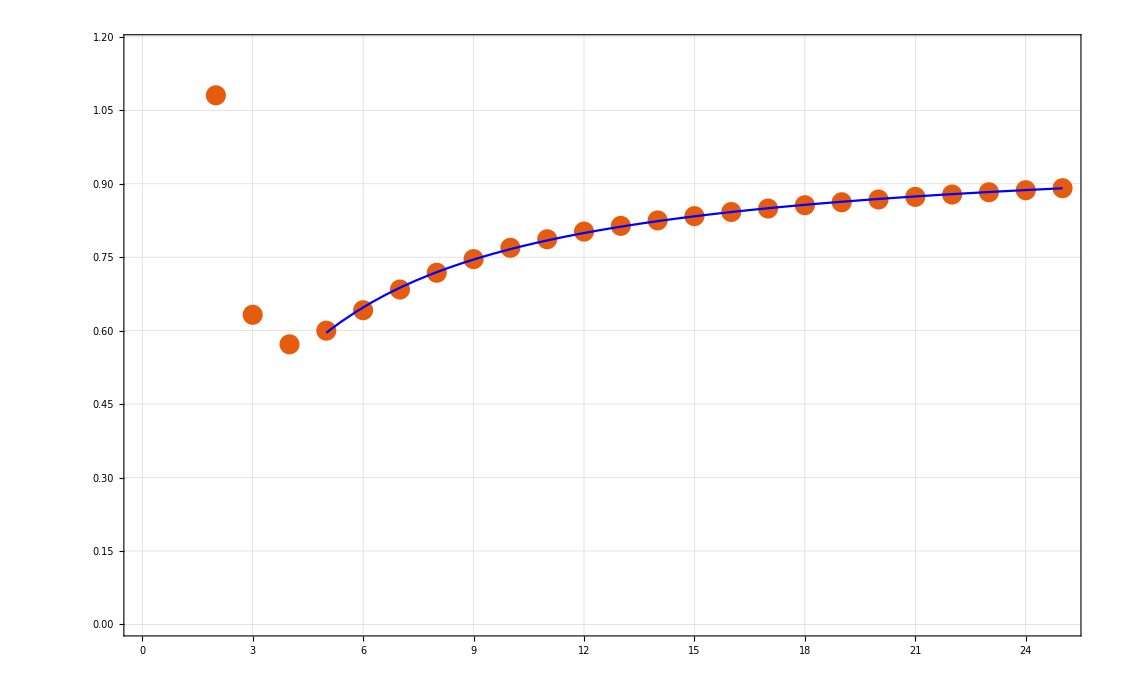

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai2[[-1]]Ai2[[-3]]-Ai2[[-2]]^2)/(Ai2[[-1]]-2Ai2[[-2]]+Ai2[[-3]])
```

9.50729×10^-34

The estimate for the upper bound is given by

```mathematica
UB=(Ai2[[-1]] - L Ai2[[-2]])/(1-L)
```

9.9058×10^-34

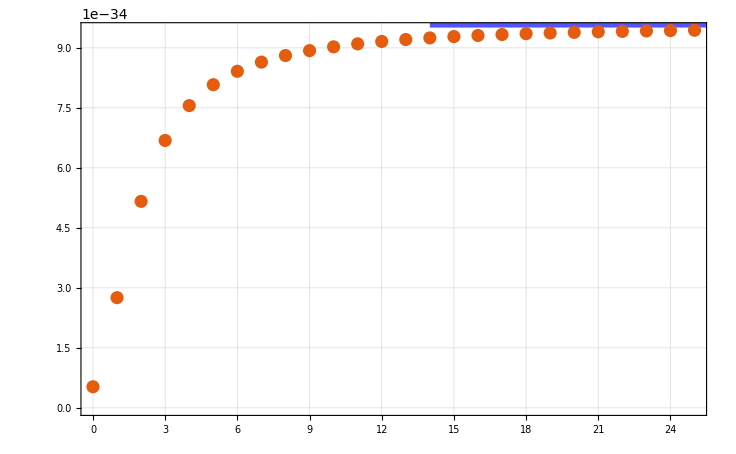

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai2}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

```mathematica
Export[ROOTDIR<>"Plots/Plotg12j1i2.svg",Ai2plot]
```

/home/pdona/Dropbox/Ongoing Projects/HowToSpinFoamAmplitude/HowToSpinFoamAmplitude/Plots/Plotg12j1i2.svg

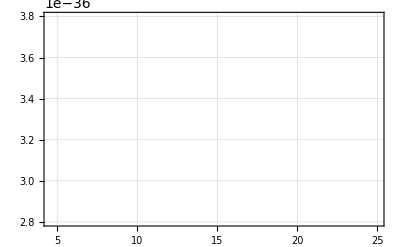

```mathematica
Ai2plot=ListPlot[Transpose[{Range[5,25],Ai2[[6;;]]}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{15,preLB},{26,preUB}],Yellow,Rectangle[{23,LB},{26,UB}]},PlotRange->{Automatic,{2.8 10^(-36),3.8 10^(-36)}}]
```

### Boundary intertwiners i = 1

```mathematica
Ai1
```

{1.05745×10^-35,5.16122×10^-35,9.14134×10^-35,1.14439×10^-34,1.26546×10^-34,1.33302×10^-34,1.37411×10^-34,1.40145×10^-34,1.42089×10^-34,1.4354×10^-34,1.44661×10^-34,1.45547×10^-34,1.46262×10^-34,1.46847×10^-34,1.4733×10^-34,1.47734×10^-34,1.48075×10^-34,1.48364×10^-34,1.48612×10^-34,1.48826×10^-34,1.49011×10^-34,1.49173×10^-34,1.49314×10^-34,1.49439×10^-34,1.4955×10^-34,1.49649×10^-34}

```mathematica
ai1n[DL_]:=If[DL==0, Ai1[[1]],Ai1[[DL+1]]-Ai1[[DL]]]
```

```mathematica
ci1n[DL_]:=ai1n[DL]/ai1n[DL-1]
```

```mathematica
ratios=Table[{DL,ci1n[DL]},{DL,1,25}]
```

{{1,3.88084},{2,0.969867},{3,0.578517},{4,0.525787},{5,0.558075},{6,0.608214},{7,0.665311},{8,0.711095},{9,0.74598},{10,0.773038},{11,0.790721},{12,0.806709},{13,0.817012},{14,0.827738},{15,0.83527},{16,0.843308},{17,0.849697},{18,0.856143},{19,0.861893},{20,0.867265},{21,0.87251},{22,0.877089},{23,0.881862},{24,0.885825},{25,0.890137}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.968854-0.769182/x^2-1.95136/x

```mathematica
L= Limit[fit,x->∞]
```

0.968854

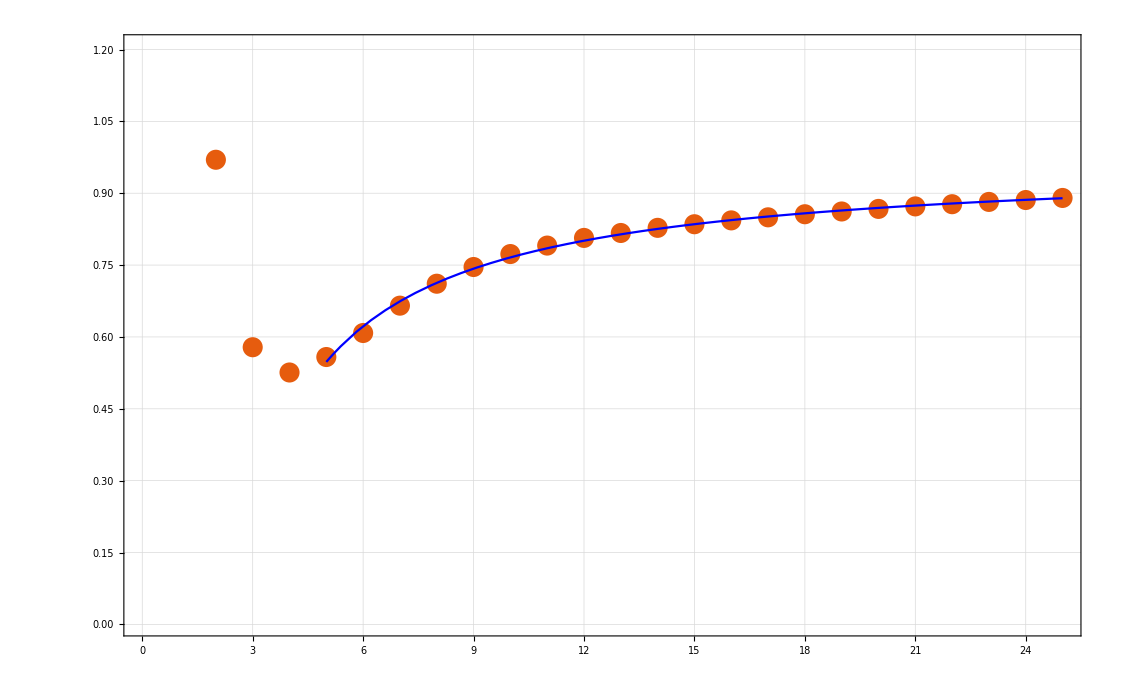

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai1[[-1]]Ai1[[-3]]-Ai1[[-2]]^2)/(Ai1[[-1]]-2Ai1[[-2]]+Ai1[[-3]])
```

1.50447×10^-34

The estimate for the upper bound is given by

```mathematica
UB=(Ai1[[-1]] - L Ai1[[-2]])/(1-L)
```

1.52715×10^-34

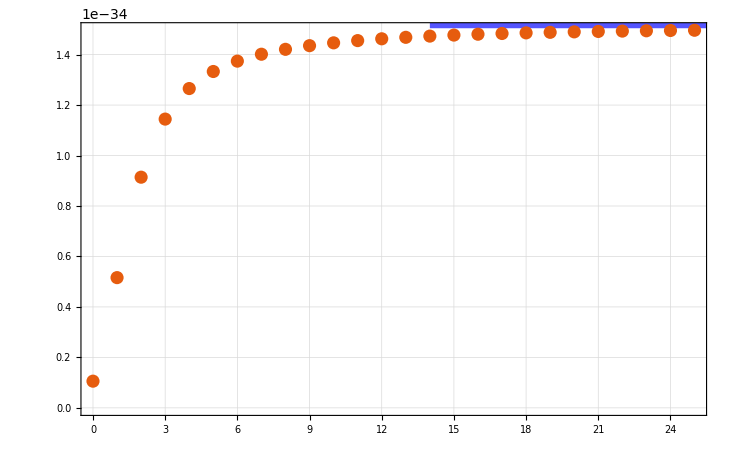

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

### Boundary intertwiners i = 0

```mathematica
Ai0
```

{2.06534×10^-36,1.09491×10^-35,2.17843×10^-35,2.98008×10^-35,3.51451×10^-35,3.87472×10^-35,4.124×10^-35,4.3023×10^-35,4.43351×10^-35,4.53267×10^-35,4.60938×10^-35,4.66991×10^-35,4.71853×10^-35,4.75815×10^-35,4.79089×10^-35,4.81823×10^-35,4.8413×10^-35,4.86094×10^-35,4.8778×10^-35,4.89238×10^-35,4.90506×10^-35,4.91617×10^-35,4.92594×10^-35,4.93459×10^-35,4.94228×10^-35,4.94915×10^-35}

```mathematica
ai0n[DL_]:=If[DL==0, Ai0[[1]],Ai0[[DL+1]]-Ai0[[DL]]]
```

```mathematica
ci0n[DL_]:=ai0n[DL]/ai0n[DL-1]
```

```mathematica
ratios=Table[{DL,ci0n[DL]},{DL,1,25}]
```

{{1,4.30139},{2,1.21965},{3,0.739858},{4,0.666666},{5,0.674008},{6,0.692044},{7,0.715221},{8,0.735983},{9,0.755623},{10,0.773717},{11,0.78894},{12,0.803341},{13,0.814951},{14,0.826115},{15,0.835205},{16,0.843945},{17,0.851327},{18,0.858321},{19,0.864501},{20,0.870225},{21,0.875505},{22,0.880285},{23,0.884856},{24,0.888918},{25,0.89291}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.998071+6.19697/x^2-2.86392/x

```mathematica
L= Limit[fit,x->∞]
```

0.998071

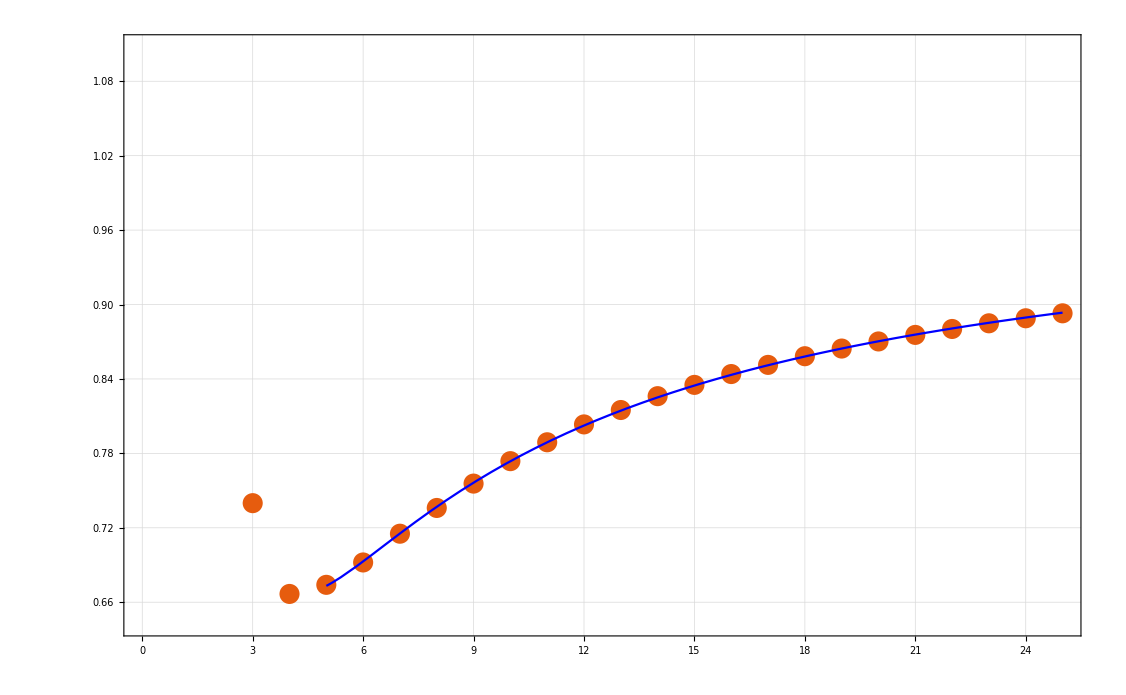

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai0[[-1]]Ai0[[-3]]-Ai0[[-2]]^2)/(Ai0[[-1]]-2Ai0[[-2]]+Ai0[[-3]])
```

5.00639×10^-35

The estimate for the upper bound is given by

```mathematica
UB=(Ai0[[-1]] - L Ai0[[-2]])/(1-L)
```

8.50126×10^-35

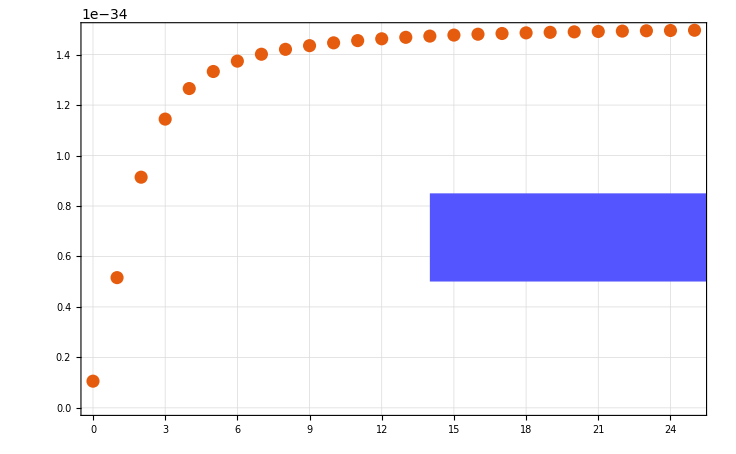

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

## Boundary spins j = 1 and γ = 0.1

We import the CSV data into the appropriate columns

```mathematica
ROOTDIR = NotebookDirectory[];
```

```mathematica
{Ai0,Ai1,Ai2}=Transpose[Import[ROOTDIR<>"Delta_4_ampls/Immirzi_0.1/j_1.0/CSV_format/Delta_4_ampls_Dl_max_25.csv","Table"]];
```

### Boundary intertwiners i = 2

```mathematica
Ai2
```

{1.73228×10^-25,8.4097×10^-25,1.64612×10^-24,2.30166×10^-24,2.78686×10^-24,3.13607×10^-24,3.38984×10^-24,3.57681×10^-24,3.71739×10^-24,3.82497×10^-24,3.90883×10^-24,3.97521×10^-24,4.02856×10^-24,4.07199×10^-24,4.10777×10^-24,4.13757×10^-24,4.16263×10^-24,4.18389×10^-24,4.20208×10^-24,4.21774×10^-24,4.23133×10^-24,4.24319×10^-24,4.2536×10^-24,4.26278×10^-24,4.27093×10^-24,4.27818×10^-24}

```mathematica
ai2n[DL_]:=If[DL==0, Ai2[[1]],Ai2[[DL+1]]-Ai2[[DL]]]
```

```mathematica
ci2n[DL_]:=ai2n[DL]/ai2n[DL-1]
```

```mathematica
ratios=Table[{DL,ci2n[DL]},{DL,1,25}]
```

{{1,3.8547},{2,1.20578},{3,0.814181},{4,0.740151},{5,0.719722},{6,0.726699},{7,0.736764},{8,0.751945},{9,0.765197},{10,0.779504},{11,0.791571},{12,0.803712},{13,0.813974},{14,0.824068},{15,0.832675},{16,0.841074},{17,0.848306},{18,0.855348},{19,0.861468},{20,0.867429},{21,0.872655},{22,0.877749},{23,0.88225},{24,0.886646},{25,0.890556}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.994048+7.83907/x^2-2.92809/x

```mathematica
L= Limit[fit,x->∞]
```

0.994048

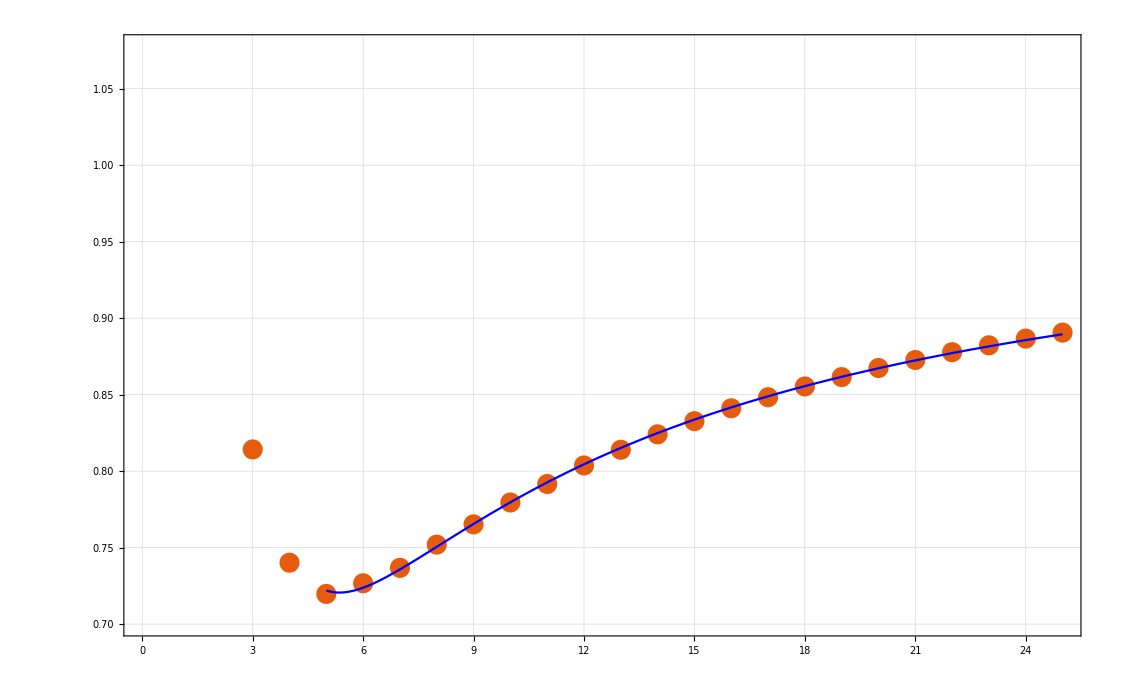

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai2[[-1]]Ai2[[-3]]-Ai2[[-2]]^2)/(Ai2[[-1]]-2Ai2[[-2]]+Ai2[[-3]])
```

4.33718×10^-24

The estimate for the upper bound is given by

```mathematica
UB=(Ai2[[-1]] - L Ai2[[-2]])/(1-L)
```

5.48912×10^-24

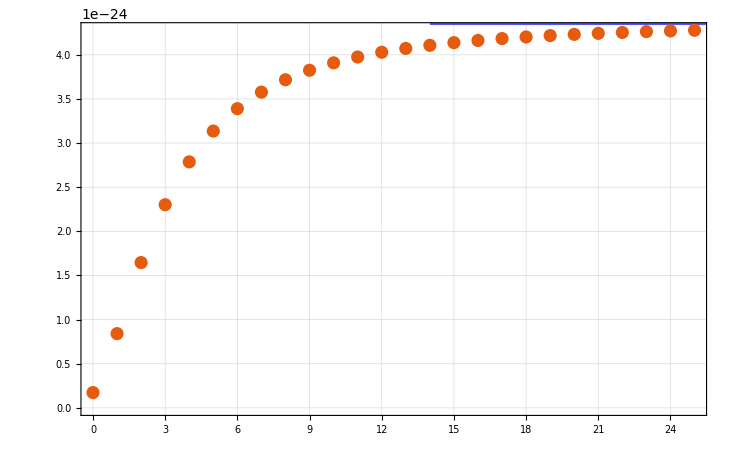

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai2}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

```mathematica
Export[ROOTDIR<>"Plots/Plotg12j1i2.svg",Ai2plot]
```

/home/pdona/Dropbox/Ongoing Projects/HowToSpinFoamAmplitude/HowToSpinFoamAmplitude/Plots/Plotg12j1i2.svg

```mathematica
Ai2plot=ListPlot[Transpose[{Range[5,25],Ai2[[6;;]]}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{15,preLB},{26,preUB}],Yellow,Rectangle[{23,LB},{26,UB}]},PlotRange->{Automatic,{2.8 10^(-36),3.8 10^(-36)}}]
```

-Graphics-

### Boundary intertwiners i = 1

```mathematica
Ai1
```

{5.95039×10^-26,2.76091×10^-25,5.21764×10^-25,7.12266×10^-25,8.48548×10^-25,9.44201×10^-25,1.01247×10^-24,1.06208×10^-24,1.099×10^-24,1.12701×10^-24,1.1487×10^-24,1.16578×10^-24,1.17945×10^-24,1.19053×10^-24,1.19964×10^-24,1.20721×10^-24,1.21355×10^-24,1.21893×10^-24,1.22352×10^-24,1.22747×10^-24,1.23089×10^-24,1.23387×10^-24,1.23649×10^-24,1.23879×10^-24,1.24083×10^-24,1.24265×10^-24}

```mathematica
ai1n[DL_]:=If[DL==0, Ai1[[1]],Ai1[[DL+1]]-Ai1[[DL]]]
```

```mathematica
ci1n[DL_]:=ai1n[DL]/ai1n[DL-1]
```

```mathematica
ratios=Table[{DL,ci1n[DL]},{DL,1,25}]
```

{{1,3.63988},{2,1.13429},{3,0.775427},{4,0.715385},{5,0.701879},{6,0.713747},{7,0.726595},{8,0.744171},{9,0.758809},{10,0.774464},{11,0.787299},{12,0.800267},{13,0.810984},{14,0.821617},{15,0.830507},{16,0.839273},{17,0.84669},{18,0.853992},{19,0.860235},{20,0.866386},{21,0.871695},{22,0.876932},{23,0.881492},{24,0.885996},{25,0.889947}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.995449+7.52284/x^2-2.96166/x

```mathematica
L= Limit[fit,x->∞]
```

0.995449

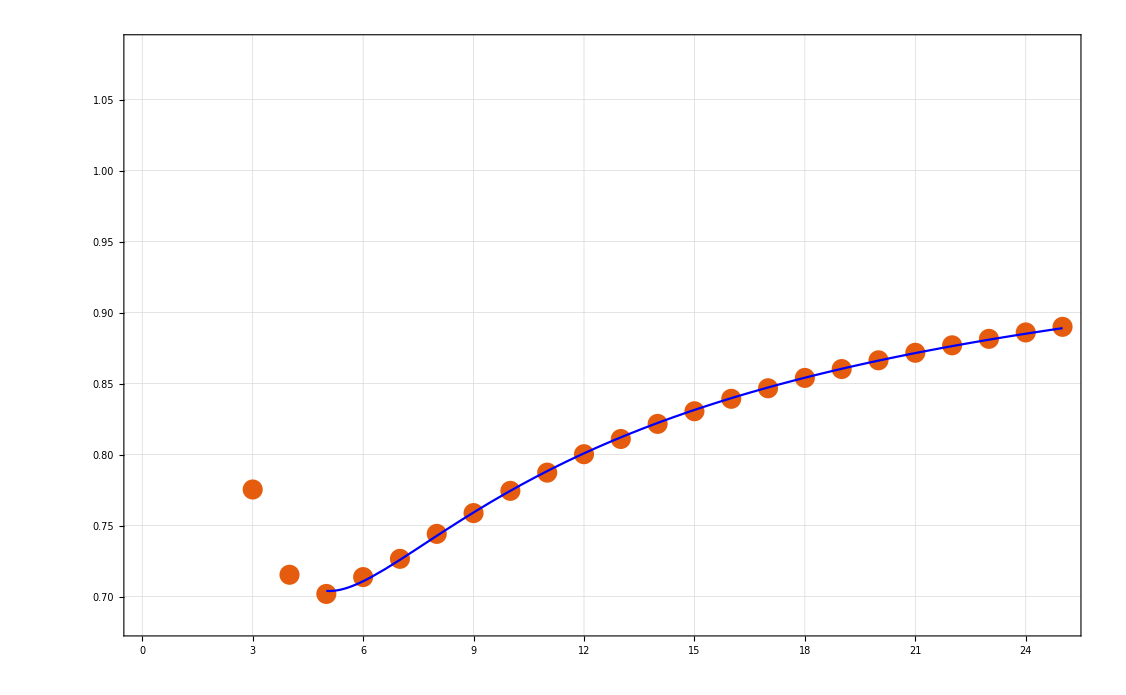

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai1[[-1]]Ai1[[-3]]-Ai1[[-2]]^2)/(Ai1[[-1]]-2Ai1[[-2]]+Ai1[[-3]])
```

1.25735×10^-24

The estimate for the upper bound is given by

```mathematica
UB=(Ai1[[-1]] - L Ai1[[-2]])/(1-L)
```

1.64022×10^-24

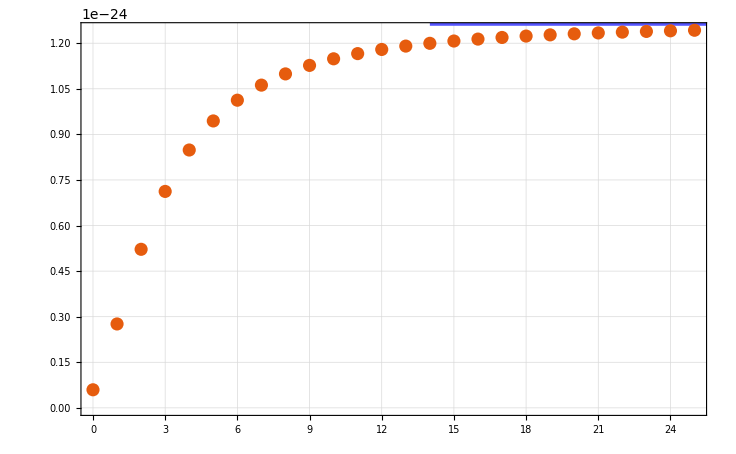

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

### Boundary intertwiners i = 0

```mathematica
Ai0
```

{8.11368×10^-27,3.87335×10^-26,7.74983×10^-26,1.11081×10^-25,1.37469×10^-25,1.57478×10^-25,1.72678×10^-25,1.84306×10^-25,1.93335×10^-25,2.00436×10^-25,2.06105×10^-25,2.10686×10^-25,2.14436×10^-25,2.17538×10^-25,2.20131×10^-25,2.22318×10^-25,2.24178×10^-25,2.25773×10^-25,2.27149×10^-25,2.28346×10^-25,2.29391×10^-25,2.30311×10^-25,2.31123×10^-25,2.31843×10^-25,2.32486×10^-25,2.33061×10^-25}

```mathematica
ai0n[DL_]:=If[DL==0, Ai0[[1]],Ai0[[DL+1]]-Ai0[[DL]]]
```

```mathematica
ci0n[DL_]:=ai0n[DL]/ai0n[DL-1]
```

```mathematica
ratios=Table[{DL,ci0n[DL]},{DL,1,25}]
```

{{1,3.77385},{2,1.266},{3,0.866309},{4,0.785782},{5,0.758269},{6,0.759619},{7,0.765046},{8,0.77641},{9,0.786572},{10,0.798258},{11,0.808184},{12,0.818465},{13,0.82719},{14,0.835923},{15,0.843394},{16,0.85077},{17,0.857141},{18,0.863398},{19,0.868852},{20,0.874199},{21,0.878899},{22,0.883506},{23,0.887587},{24,0.891588},{25,0.895158}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.987645+7.58604/x^2-2.65125/x

```mathematica
L= Limit[fit,x->∞]
```

0.987645

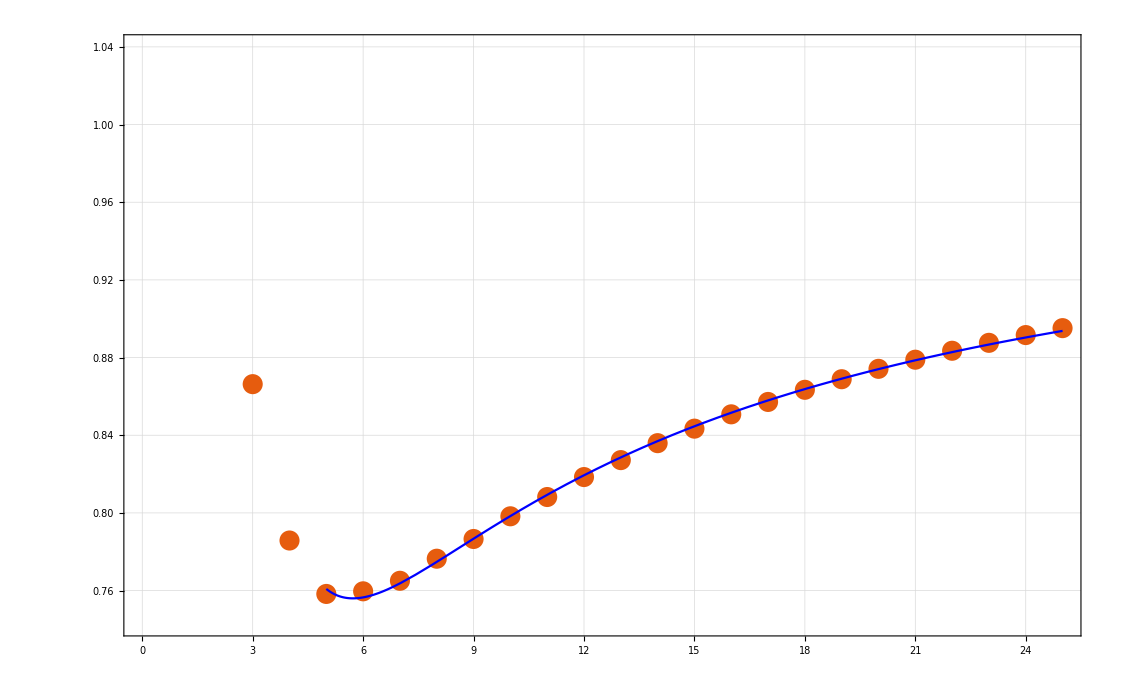

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai0[[-1]]Ai0[[-3]]-Ai0[[-2]]^2)/(Ai0[[-1]]-2Ai0[[-2]]+Ai0[[-3]])
```

2.37973×10^-25

The estimate for the upper bound is given by

```mathematica
UB=(Ai0[[-1]] - L Ai0[[-2]])/(1-L)
```

2.79046×10^-25

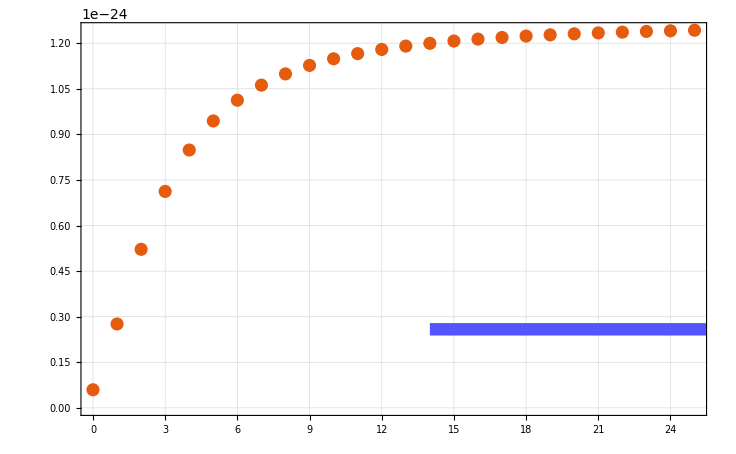

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai1}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```